```mathematica
r[t_]:=a t^5+b t^4+c t^3+d t^2+e t+f
```

```mathematica
res=Solve[{
r[0]==x0,
r'[0]==v0,
r''[0]==a0,
r[tf]==xf,
r'[tf]==vf,
r''[tf]==af
},{a,b,c,d,e,f}][[1]]
```

{a→-(a0 tf^2-af tf^2+6 tf v0+6 tf vf+12 x0-12 xf)/(2 tf^5),b→-(-3 a0 tf^2+2 af tf^2-16 tf v0-14 tf vf-30 x0+30 xf)/(2 tf^4),c→-(3 a0 tf^2-af tf^2+12 tf v0+8 tf vf+20 x0-20 xf)/(2 tf^3),d→a0/2,e→v0,f→x0}

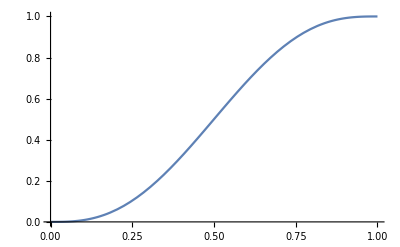

```mathematica
data={x0->0,v0->0,a0->0,xf->1,vf->0,af->0,tf->1};
Plot[{r[t]/.res/.data},{t,0,1}]
```

```mathematica
Simplify[Solve[r''[t]==0,t]/.res/.data]
```

{{t→1},{t→0},{t→1/2}}